```mathematica
SetDirectory[FileNameJoin[{$PACKAGES}]]
Import["absorption.wl"]
Import["fileManipulation.wl"]
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesEvery10"]
```

C:\Users\kahrendsen2\Box Sync\Research\mathematicaRb\packages

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesEvery10

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_110027.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0224,CVGauge(N2)(Torr)→0.279,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→132.2,SetTemp(Res)→135.,CurrTemp(Targ)→160.3,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 11:00:27GMT-6.

Quantity::unkunit: Unable to interpret unit specification 11:00:27.

Quantity::unkunit: Unable to interpret unit specification 11:10:26.

Quantity::unkunit: Unable to interpret unit specification 11:20:27.

General::stop: Further output of Quantity::unkunit will be suppressed during this calculation.

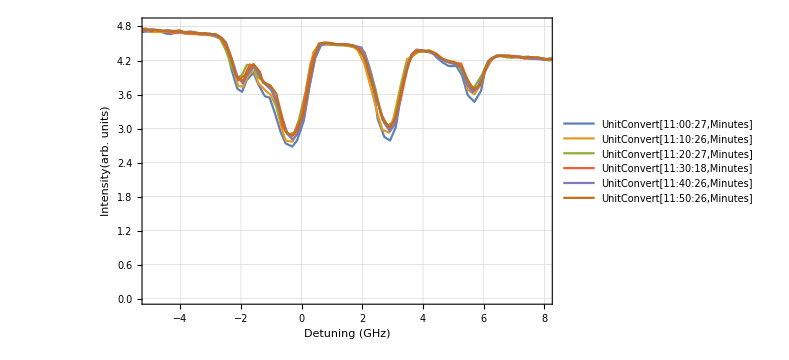

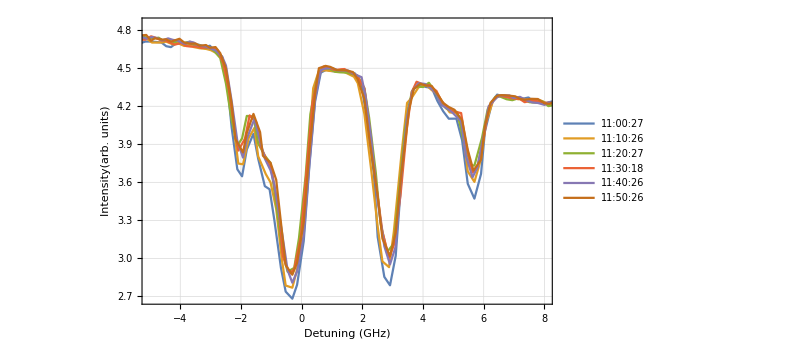

```mathematica
fn=fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,DateString[t2,{"Time"}]];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{0,Automatic}},PlotLegends->{SetPrecision[UnitConvert[legendLabels,"Minutes"],2]},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"}]
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->{legendLabels},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"}]
```

```mathematica
DateString[t2,{"Time"}]
```

11:50:26

```mathematica
fn=FileNames["*.dat"];
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
data=ImportFile[fn[[2]]];
h=data[[1]]
t2=ExtractTimeInfoFromFileNameString[h["Filename"]]
deltat=t2-t1

d=data[[2]]
plotd=Select[d[All,{"DET","VERT"}],#DET<100&];
AppendTo[plots,plotd];
```

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_110027.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0224,CVGauge(N2)(Torr)→0.279,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→132.2,SetTemp(Res)→135.,CurrTemp(Targ)→160.3,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 11:00:27GMT-6.

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_111026.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0224,CVGauge(N2)(Torr)→0.282,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→136.6,SetTemp(Res)→135.,CurrTemp(Targ)→160.2,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 11:10:26GMT-6.

9.98333 min

Dataset[<>]

```mathematica
j=1;
data=ImportFile[fn[[j]]];

d=data[[2]];
d[All,{"DET","VERT"}]
plotd=Select[d[All,{"WAV","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
```

Dataset[<>]

Function::slot1: (#DET>-100&)[Dataset] is expected to have an Association as the first argument.

Function::slota: Named Slot DET in #DET>-100& cannot be filled from <|MessageTemplate:>Dataset::partnotapplicable,MessageParameters→<|Type→TypeSystem`Struct[{VOLT,DET,VERT,VERTsd,HORIZ,HORIZsd,REF,REFsd},{TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→{WAV,VERT},Symbol→Part|>|>.

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesEvery10

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_110027.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0224,CVGauge(N2)(Torr)→0.279,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→132.2,SetTemp(Res)→135.,CurrTemp(Targ)→160.3,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 11:00:27GMT-6.

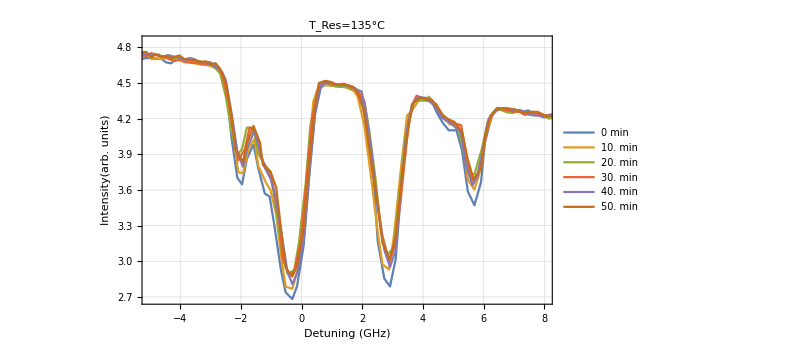

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesEvery10"]
fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,t2-t1];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->{SetPrecision[UnitConvert[legendLabels,"Minutes"],2]},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"},PlotLabel->"T_Res=135°C"]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesEvery10_T=140

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_122026.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0226,CVGauge(N2)(Torr)→0.278,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→132.1,SetTemp(Res)→140.,CurrTemp(Targ)→160.1,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 12:20:26GMT-6.

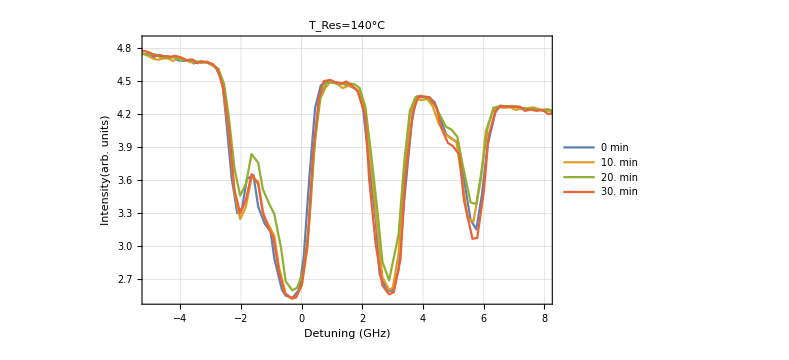

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesEvery10_T=140"]
fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,t2-t1];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->{SetPrecision[UnitConvert[legendLabels,"Minutes"],2]},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"},PlotLabel->"T_Res=140°C"]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesEvery10_T=145

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_130027.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0228,CVGauge(N2)(Torr)→0.279,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→144.5,SetTemp(Res)→145.,CurrTemp(Targ)→160.5,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 13:00:27GMT-6.

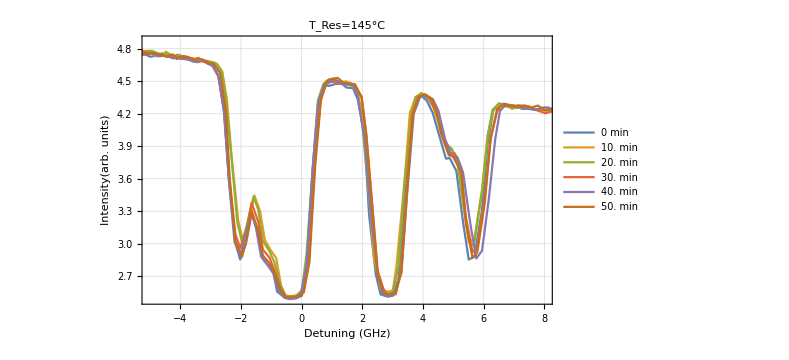

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesEvery10_T=145"]
fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,t2-t1];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->{SetPrecision[UnitConvert[legendLabels,"Minutes"],2]},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"},PlotLabel->"T_Res=145°C"]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesEvery10_T=150

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_140027.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0227,CVGauge(N2)(Torr)→0.282,CVGauge(He)(Torr)→0.0000891,CurrTemp(Res)→145.1,SetTemp(Res)→150.,CurrTemp(Targ)→163.8,SetTemp(Targ)→165.,CurrTemp(Res2)→165.,SetTemp(Res2)→165.|>

Tue 18 Dec 2018 14:00:27GMT-6.

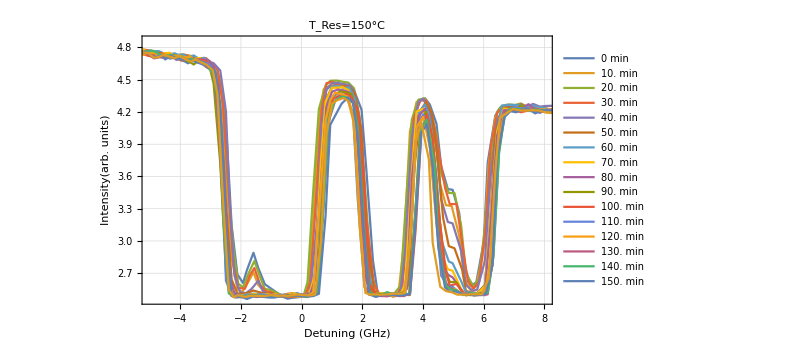

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesEvery10_T=150"]
fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,t2-t1];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->{SetPrecision[UnitConvert[legendLabels,"Minutes"],2]},FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"},PlotLabel->"T_Res=150°C"]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data\profilesTBiggerThan130

<|Filename→/home/pi/RbData/2018-12-18/RbAbs2018-12-18_104026.dat,Comments→RbAutoScan,IonGauge(Torr)→0.0226,CVGauge(N2)(Torr)→0.28,CVGauge(He)(Torr)→0.0000892,CurrTemp(Res)→130.,SetTemp(Res)→130.,CurrTemp(Targ)→159.6,SetTemp(Targ)→160.,CurrTemp(Res2)→160.,SetTemp(Res2)→160.|>

Tue 18 Dec 2018 10:40:26GMT-6.

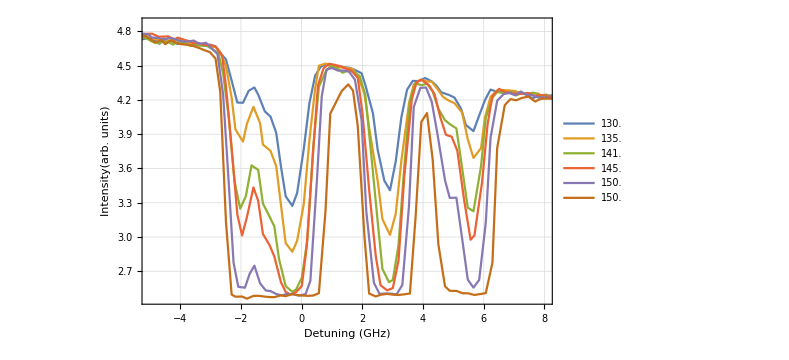

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\2018-12-14\\data\\profilesTBiggerThan130"]
fn=FileNames["*.dat"];
plots={};
legendLabels={};
data=ImportFile[fn[[1]]];
h=data[[1]]
t1=ExtractTimeInfoFromFileNameString[h["Filename"]]
For[j=1,j≤Length[fn],j++,
data=ImportFile[fn[[j]]];
h=data[[1]];
d=data[[2]];
t2=ExtractTimeInfoFromFileNameString[h["Filename"]];
plotd=Select[d[All,{"DET","VERT"}],#DET>-100&];
AppendTo[plots,plotd];
AppendTo[legendLabels,h["CurrTemp(Res)"]];
];
ListLinePlot[plots,Joined->True,PlotRange->{{-5,8},{Automatic,Automatic}},PlotLegends->SetPrecision[legendLabels,3],FrameLabel->{"Detuning (GHz)","Intensity(arb. units)"}]
```